```mathematica
f[x_] := (Binomial[6, 3 - x] * Binomial[4, x]) / Binomial[10, 3]
```

```mathematica
g[y_] := Sum[f[x], {x, 0, y}]
```

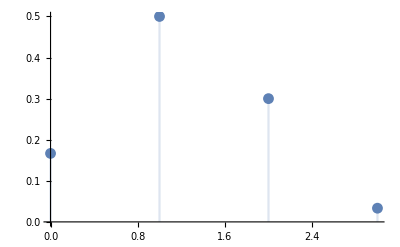

```mathematica
DiscretePlot[f[x], {x, 0, 3}]
```

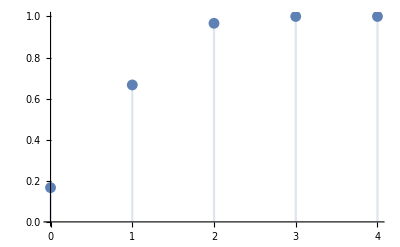

```mathematica
DiscretePlot[g[x], {x, 0, 4}]
```

```mathematica
f[x] := x / 2
```

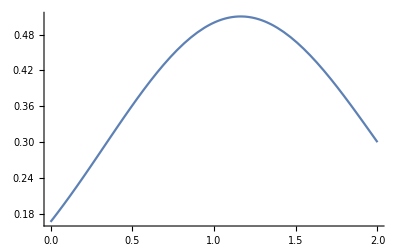

```mathematica
Plot[f[x], {x, 0, 2}]
```

```mathematica
f[x_] := x / 2
```

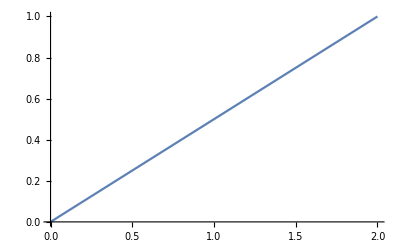

```mathematica
Plot[f[x], {x, 0, 2}]
```

```mathematica
g[y_] = Integrate[f[x], {x, 0, y}]
```

y^2/4

```mathematica
Plot[g[y_], {y, 0, 2}]
```

-Graphics-

```mathematica
Plot[g[y], {y, 0, 2}]
```

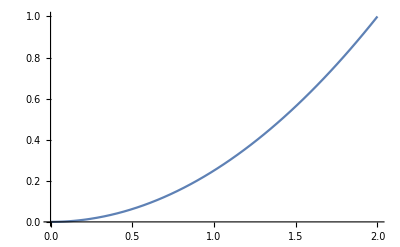

```mathematica
e[x_] := Integrate[x * f[x], {x, 0, 2}]
```

```mathematica
e[1]
```

Integrate::ilim: Invalid integration variable or limit(s) in {1, 0, 2}.

∫_0^2 1/2 ⅆ1

```mathematica
Integrate[x * f[x], {x, 0, 2}]
```

4/3

```mathematica
0.2+0.25+0.3+0.1
```

0.85

```mathematica
1 - 0.85
```

0.15

```mathematica
0.2*0 + 0.25*1+0.3*2+0.15*3+0.1*4
```

1.7

```mathematica
Integrate[1.25*(1-x^4), {x, 0, 1}]
```

1.

```mathematica
1 - Integrate[1.25*(1-x^4), {x, 0, 0.8}]
```

0.08192

```mathematica
Integrate(
```

```mathematica
g[y_] := Integrate[1.25*(1-x^4), {x, 0, y}]
```

```mathematica
g[y]
```

0.+1.25 y-0.25 y^5

```mathematica
Integrate[1.25*(1-x^4), {x, 0.6, 0.8}]
```

0.18752

```mathematica
Integrate[1.25*(1-x^4)*x, {x, 0, 1}]
```

0.416667

```mathematica
Integrate[1.25*(1-x^4)*(x - 0.4166)^2, {x, 0, 1}]
```

```mathematica
0.0644841314285714
3/7*0.3
```

0.0644841

0.128571

```mathematica
0.3*3/7+4/7*0.3
```

0.3

```mathematica
3/7*0.4+4/7*0.5
```

0.457143

```mathematica
4/7*0.2
```

0.114286

```mathematica
0.128+0.3+0.4571+0.114
```

0.9991

```mathematica
0.128+0.3
```

0.428

```mathematica
0.428 + 0.4571
```

0.8851

```mathematica
0.4571+0.3+0.128
```

0.8851

```mathematica
Integrate[x, {x, 0, 1}] + Integrate[1, {x, 1, 1.5}]
```

1.

```mathematica
(Sqrt[0]*0.2+Sqrt[1]*0.25+Sqrt[2]*0.3+Sqrt[3]*0.15+Sqrt[4]*0.1) + 0.3*1.7
```

1.64407

```mathematica
Integrate[x, {x, 0, 0.8}]
```

0.32

```mathematica
1 - Integrate[x, {x, 0, 1}]
```

1/2

```mathematica
Integrate[x, {x, 0, 1}] + Integrate[1, {x, 1, 1.3}]
```

0.8

```mathematica
g[y_] := Integrate[x, {x, 0, y}] + Integrate[1, {x, 1, y}]
```

```mathematica
g[y]
```

-1+y+y^2/2

```mathematica
g[0.8]
```

0.12

```mathematica
Integrate[x, {x, 0, 0.8}]
```

0.32

```mathematica
g[y_] := Integrate[x, {x, 0, y}]
```

```mathematica
g[y]
```

y^2/2

```mathematica
g[y_] := Integrate[x, {x, 0, 1}] + Integrate[1, {x, 1, y}]
```

```mathematica
g[y]
```

-1/2+y

```mathematica
o.8^2/2
```

```mathematica
4
```

4

```mathematica
1.3-1/2
```

0.8

```mathematica
Integrate[x*x, {x, 0, 1}] + Integrate[x, {x, 1, 1.5}]
```

0.958333

```mathematica
Integrate[x]
```

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

Integrate[x]

```mathematica
Integrate[x*x, {x, 0, 1}] + Integrate[x, {x, 1, 1.5}]
```

0.958333

```mathematica
1.25*(0.5-(0.5^5/5))
```

0.617188

```mathematica
1 - 1.25*(0.5-(0.5^5/5))
```

```mathematica
0.3828125
```

0.382813

```mathematica
Integrate[x/2, {x, 0, 1.4}]
```

```mathematica
4*9
```

36